# 2. domača naloga

## 1. naloga

a)  Definirajte funkcijo , ki sprejme naravni števili  in  in vrne matriko dimenzije , kjer se na vsakem mestu v matriki pojavi vsota indeksa stolpca in indeksa vrstice.
b) Izračunajte lastne vrednosti in lastne vektorje matrike .
c)  Narišite lastne vektorje matrike .

d) Izračunajte karakteristični polinom matrike .
e) Matriko  diagonalizirajte. Določite ustrezno diagonalno matriko , prehodno matriko  in .
f) Rešite matrično enačbo .

```mathematica
A[n_,m_]:=Table[i+j,{i,1,n},{j,1,m}]
A[3,3]
```

```mathematica
{{2,3,4},{3,4,5},{4,5,6}}


mat=A[3,3];
eigenvalues=Eigenvalues[mat]
eigenvectors=Eigenvectors[mat]
```

{{2,3,4},{3,4,5},{4,5,6}}

{6+√42,6-√42,0}

{{-(-17-2 √42)/(23+4 √42),-(-20-3 √42)/(23+4 √42),1},{-(17-2 √42)/(-23+4 √42),-(20-3 √42)/(-23+4 √42),1},{1,-2,1}}

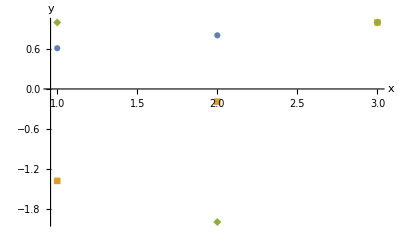

```mathematica
ListPlot[eigenvectors,PlotStyle->PointSize[Large],AxesLabel->{"x","y"},PlotRange->All,PlotMarkers->Automatic]
```

```mathematica
ListPointPlot3D[eigenvectors,PlotStyle->PointSize[Large]]
```

-Graphics3D-

```mathematica
CharacteristicPolynomial[mat,λ]
```

6 λ+12 λ^2-λ^3

```mathematica
{vals,vecs}=Eigensystem[mat];
P=Transpose[vecs]; (*Stolpci so lastni vektorji*)
G=DiagonalMatrix[vals];
Pinv=Inverse[P];
```

```mathematica
Simplify[P.G.Pinv==mat]
```

True

```mathematica
lhs=mat+P-G;
X=LinearSolve[lhs,IdentityMatrix[3]]
```

{{(97-21 √42)/(3 (-27+26 √42)),(3023-382 √42)/(3 (-27+26 √42) (-184+27 √42)),(28463-4467 √42)/(3 (-27+26 √42) (-184+27 √42))},{((-23+4 √42) (278+45 √42))/(132 (-27+26 √42)),(-22949+2690 √42)/(6 (-27+26 √42) (-184+27 √42)),(13966-1715 √42)/(6 (-27+26 √42) (-184+27 √42))},{(-184+27 √42)/(6 (-27+26 √42)),-(2 (64+7 √42))/(3 (-27+26 √42)),(218+15 √42)/(6 (-27+26 √42))}}

## 2. naloga

Imamo klančino z naklonom 30 stopinj dolžine 10m. Na dnu klančine se nahaja ravnina dolžine 10m. Na levem in desnem robu se nahaja stena (glej sliko). 
Kroglico z radijem 10cm spustimo na vrhu klanca, da se začne gibati pod vplivom gravitacije. Predpostavite lahko, da med kroglico in podlago ni trenja in 
da se zaradi kotaljenja energija ne izgublja. Ko pride kroglica na dno klanca, se giblje v vodoravni smeri z enako velikim vektorjem hitrosti (predpostavi, 
da je kot dovolj majhen, da na pride do odboja). 
Simulirajte kotaljenje kroglice po klančini in ravnini, ki se odbija od desnega roba.
Za gravitacijski pospešek vzemite g = 9.81, začetna hitrost kroglice naj bo v0 = 0.

a) Definiraj gravitacijski pospešek, naklon, dolžino klanca, začetno hitrost in radij kroglice.

```mathematica
g=9.81; (*gravitacijski pospešek*)
α=30 Degree; (*naklon*)
L1=10; (*dolžina klanca*)
L2=10; (*dolžina ravnine*)
v0=0; (*začetna hitrost*)
r=1; (*radij krogle*)
```

b) Nariši klančino, tla in obe steni.

```mathematica
risanjeOkolja:=Graphics[{Thick,Line[{{0,0},{L1 Cos[α],L1 Sin[α]},{L1 Cos[α]+L2,L1 Sin[α]},{L1 Cos[α]+L2,0}}],Line[{{0,0},{0,20}}],Line[{{L1 Cos[α]+L2,0},{L1 Cos[α]+L2,20}}]}]
```

c) Na sliko dodaj kroglico tako, da se bo kroglica premaknila, če se spremeni njeno središče.

```mathematica
kroglica[x_,y_]:=Graphics[{Red,Disk[{x,y},r]}]
```

d) Definiraj funkcijo `naKlancu`, ki sprejme središče kroglice in vrne `True`, če je kroglica na klancu.

```mathematica
naKlancu[{x_,y_}]:=y>0
```

e) Definiraj funkcijo `desniRob`, ki sprejme središče kroglice in vrne `True`, če je kroglica trčila ob desni rob.

```mathematica
desniRob[{x_,y_}]:=x+r>=L1 Cos[α]+L2
```

f) Definiraj funkcijo `posodobiHitrost`, ki sprejme vektor trenutne hitrost kroglice in kot α ter vrne novo hitrost, gibanja po klančini z naklonom α.

```mathematica
posodobiHitrost[v_,t_,α_]:=v+g*Sin[α]*t
```

g) Definiraj funkcijo `hitrostNaKlanec`, ki sprejme vektor trenutne hitrosti kroglice in kot α ter vrne novo hitrost, ki jo dobi kroglica, ko iz ravnega dela preide na klanec z naklonom α.

```mathematica
hitrostSKlanca[v_]:={v*Cos[α],0}
```

h) Definiraj funkcijo `hitrostSKlanca`, ki sprejme vektor trenutne hitrosti kroglice in vrne novo hitrost, ki jo dobi kroglica, ko s klanca preide na ravni del.

```mathematica
hitrostSKlanca[v_]:={v*Cos[α],0}
```

i) S pomočjo prejšnjih funkcij simuliraj premikanje kroglice.

```mathematica
simulacijaKrogle:=Module[{dt=0.05,t=0,v=v0,pos={0,0},traj={},vmax=0},While[!desniRob[pos],If[naKlancu[pos],v=posodobiHitrost[v,dt,α];
pos+=dt*hitrostNaKlancu[v],pos+=dt*hitrostSKlanca[v]];
AppendTo[traj,pos];
t+=dt;
vmax=Max[vmax,v];];
traj]
```

```mathematica
trajektorija=simulacijaKrogle;
frames=Table[Show[risanjeOkolja,kroglica[trajektorija[[i,1]],trajektorija[[i,2]]],PlotRange->{{-1,L1 Cos[α]+L2+1},{-1,6}}],{i,1,Length[trajektorija],1}];

ListAnimate[frames]
```